# Reposiciones

## Parcial I

## Pregunta I

Resolvemos la ecuación de manera exacta:

De la expresión de la solución, es evidente que la solución es real en el intervalo . Graficamos el campo de pendientes para encontrar la solución de manera gráfica:

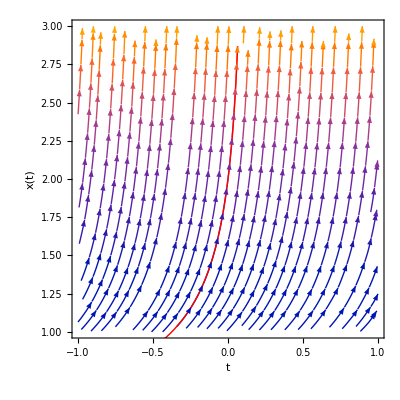

```mathematica
Show[{StreamPlot[{1,x^3},{t,-1,1},{x,1,3},FrameLabel->{t,x[t]}],Plot[2*Sqrt[1/(1-8*t)],{t,-1,1/8},PlotStyle->{Red,Thick}]}]
```

De aquí vemos que . Esto también se puede ver desde el espacio fase

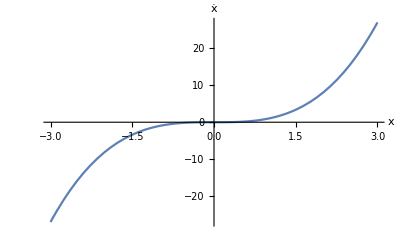

```mathematica
Plot[x^3,{x,-3,3},AxesLabel->{x,OverDot[x]}]
```

Donde se ve que las soluciones con condiciones iniciales positivas siempre son crecientes sin tender a ninguna solución de equilibrio.

## Pregunta II

Recordamos que una solución de equilibrio  en un sistema dinámico continuo unidimensional  es asintóticamente estable si  . En otras palabras, la pendiente de la recta tangente en el punto de equilibrio debe ser negativa. Geométricamente, esto quiere decir que la gráfica de  debe cruzar el eje  de arriba hacia abajo. Si la ecuación diferencial cumple con el teorema de existencia y unicidad, entonces  es continua y diferenciable. Entonces, si  cruza el eje  de arriba hacia abajo en dos puntos, necesariamente debe cruzar el eje  de abajo hacia arriba en un punto intermedio, es decir, debe haber un punto de equilibrio inestable entre ellas. De otra manera, esto quería decir que la función  cambia de signo de positivo a negativo, y después se vuelve positiva de nuevo sin cruzar el eje . Esto sólo sería posible si  tuviera una discontinuidad de salto en un punto intermedio, pero entonces no sería continua y no cumpliría con el teorema de existencia y unicidad.

## Pregunta III

De la figura se observa que  y  son soluciones constantes de la ecuación, por lo que son soluciones de equilibrio. Vemos que  atrae a otras soluciones, mientras que  las repele, por lo que son estable e inestable, respectivamente. Cualquier ecuación que cumpla con estas condiciones es correcta. Por ejemplo,  es una opción, como se puede comprobar con sus soluciones:

NDSolve::ndsz: At t == 4.61511, step size is effectively zero; singularity or stiff system suspected.

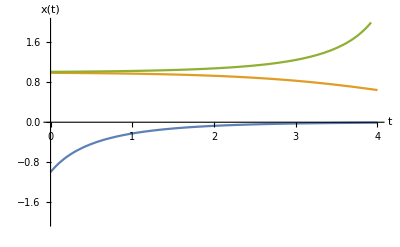

```mathematica
sol1=NDSolve[{x'[t]==x[t]^2-x[t],x[0]==-1},x,{t,0,5}];
sol2=NDSolve[{x'[t]==x[t]^2-x[t],x[0]==0.99},x,{t,0,5}];
sol3=NDSolve[{x'[t]==x[t]^2-x[t],x[0]==1.01},x,{t,0,5}];
Plot[{Evaluate[x[t]/.sol1],Evaluate[x[t]/.sol2],Evaluate[x[t]/.sol3]},{t,0,4},AxesLabel->{t,x[t]},PlotRange->{Automatic,{-2,2}}]
```

Otra opción sería la ecuación , cuyas soluciones se ven de la siguiente forma:

NDSolve::ndsz: At t == 7.97928, step size is effectively zero; singularity or stiff system suspected.

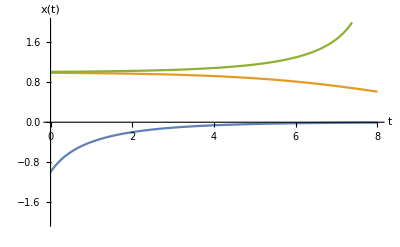

```mathematica
sol4=NDSolve[{x'[t]==Cosh[x[t]-0.5]-1.12763,x[0]==-1},x,{t,0,8}];
sol5=NDSolve[{x'[t]==Cosh[x[t]-0.5]-1.12763,x[0]==0.99},x,{t,0,8}];
sol6=NDSolve[{x'[t]==Cosh[x[t]-0.5]-1.12763,x[0]==1.01},x,{t,0,8}];
Plot[{Evaluate[x[t]/.sol4],Evaluate[x[t]/.sol5],Evaluate[x[t]/.sol6]},{t,0,8},AxesLabel->{t,x[t]},PlotRange->{Automatic,{-2,2}}]
```

## Parcial II

## Pregunta I

Para comprobar el tipo de bifurcación necesitamos comprobar el número de puntos de equilibrio y su estabilidad. En este caso los puntos de equilibrio son:


Al elevar a la , el resultado siempre es positivo si  es par, mientras que el resultado mantiene su signo original si  es impar, por lo que:
, , 
, , 
Vemos entonces que, cuando  es par, no tenemos puntos de equilibrio cuando , tenemos un sólo punto de equilibrio cuando , y tenemos dos puntos de equilibrio cuando , por lo que ocurre una bifurcación de silla nodo en .
Por otro lado, cuando  es impar, siempre tenemos sólo un punto de equilibrio. Además si calculamos su estabilidad obtenemos: 



Como  y  tienen el mismo signo, entonces , y el punto de equilibrio siempre es estable, por lo que no cambia su estabilidad, y no hay bifurcación.

En este caso, los puntos de equilibrio son

Vemos que, independientemente de  y , . Prosiguiendo


Por los mismos argumentos que en el inciso anterior, si  es par, entonces  es impar, el signo de  se conserva, y tenemos una única solución distinta de cero. Por otro lado, si  es impar, entonces  es par y tenemos dos soluciones, es decir, los puntos de equilibrio son:

, , 
, , 
Comprobamos que las soluciones de equilibrio intercambien estabilidad en el punto de bifurcación. Éste debe ser  ya que en éste ambos puntos coinciden. La estabilidad en este caso está dada por . Evaluamos en el primer punto de equilibrio que es común para todos los casos, y obtenemos , por lo que es estable si  e inestable si .
La estabilidad de los demás puntos de equilibrio está dada por: 

Vemos que, en el caso de  par, el otro punto de equilibrio siempre existe y como , , entonces el segundo punto de equilibrio es estable cuando  y es inestable cuando , al contrario que con el cero, por lo que sí intercambian estabilidad.
En el caso de  impar, los puntos de equilibrio sólo existen si  es no negativa. Por lo que, por los mismos criterios anteriores, siempre son estables cuando existen, así que la bifurcación es de tridente supercrítica.

Cambiamos los signos

Viendo las cuentas de los incisos anteriores, el signo afecta al valor de los puntos de equilibrio y al cálculo de la estabilidad. 
Para el primer inciso, el punto de equilibrio sigue existiendo siempre para  impar, pero los puntos de equilibrio sólo existen para  en el caso de  par. La estabilidad está dada en este caso por 

por lo que para  impar, el punto de equilibrio siempre es inestable.
Para el segundo inciso, la estabilidad del punto de equilibrio no cambia, pero los puntos de equilibrio  sólo existen en el caso de  impar para , que es cuando el cero es estable, por lo que la bifurcación se convierte en una bifurcación de tridente subcrítica. Para el caso de  par, la estabilidad del segundo punto de equilibrio es  
,
por lo que, al igual que en el caso anterior, es estable cuando , y es inestable cuando , por lo que sigue siendo una bifurcación transcrítica, con los mismos rangos de estabilidad para ambos puntos de equilibrio.

## Pregunta II

Los puntos de equilibrio están dados por 

Vemos que los puntos de equilibrio existen sólo si



 ó ,
por lo que deberían haber dos bifurcaciones de silla nodo en  y . En efecto, vemos que si , entonces , y si , , por lo que las soluciones en este punto aparecen o se aniquilan.

Los puntos de equilibrio son



Como los dos puntos de equilibrio siempre existen, debería haber una bifurcación transcrítica. Para asegurarnos y encontrar el punto crítico, determinamos la estabilidad. Tenemos que . Evaluando en el primer punto de equilibrio, obtenemos que 

por lo que este punto de equilibrio es estable si  e inestable si .
Con el segundo punto de equilibrio obtenemos

así que este punto de equilibrio es estable si  e inestable si . Vemos entonces que el punto crítico donde ocurre la bifurcación transcrítica es , y el parámetro  no es bifurcante.

En este caso sólo hay un punto de equilibrio que podemos calcular con facilidad, que es . Para saber donde ocurre la bifurcación, aproximamos la función cerca de este punto de equilibrio, es decir, expandimos en series de Taylor cerca de . En este caso, como es un polinomio, no tenemos que hacer la expansión por la definición, sólo notamos que, cerca de , los términos  y  son casi cero, en comparación con los otros dos términos, por lo que tenemos

Esta es la forma normal de la bifurcación transcrítica. Vemos que el otro punto de equilibrio tiene aproximadamente el valor , y calculando el criterio de estabilidad para el primer punto, encontramos que el punto crítico es , mismo punto donde .

## Pregunta 3

Puntos de equilibrio y bifurcación de silla nodo

Hacemos lo siguiente:



Hacemos el cambio de variable 



Sustituimos el cambio de variable


son cuatro puntos de equilibrio, con cada combinación diferente de signos.
Vemos para que valores de  los puntos de equilibrio ya no existen, lo cual señala una bifurcación de silla-nodo:



En esta región las soluciones no son reales. Cuando  vemos que de los cuatro  puntos de equilibrio, sólo tenemos dos,  y , por lo que cada par de puntos de equilibrio están en el punto de bifurcación de silla-nodo (recordemos que, en la bifurcación de silla nodo, tenemos una región donde no existen, otra donde surgen como uno solo, y otra donde hay dos, en este caso tenemos un par de bifurcaciones de silla nodo, por lo que en cierta región no hay puntos de equilibrio, después hay dos, y después se dividen en cuatro).
Hay otra región donde las soluciones de equilibrio ya no son reales, que es cuando 




.
Cuando , vemos que dos de estos puntos de equilibrio no son cero y tienen los valores , y los otros dos puntos de equilibrio se vuelven cero, por lo que tenemos tres puntos de equilibrio que coinciden: el cero que calculamos al principio, y los otros dos puntos de equilibrio que surgen detener signo negativo dentro y , por lo que esta NO es una bifurcación de silla-nodo, sino de tridente. Por lo tanto .

Espacio fase

Cuando , ya sabemos que sólo debe haber un cruce con el eje  porque sólo hay un punto de equilibrio. Sólo basta determinar si cruza de arriba hacia abajo o de abajo hacia arriba. Para , el término que domina es . Por lo tanto, si ,  y viceversa para . Por lo tanto, la función  debe cruzar de arriba hacia abajo. Por esta razón, el equilibrio debe ser estable. El espacio fase debe verse similar al siguiente:

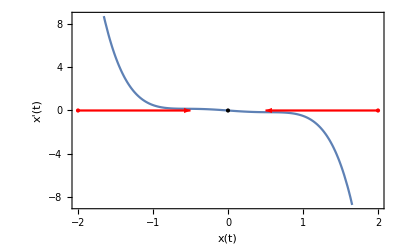

```mathematica
Show[Plot[-(1/2)*u+u^3-u^5,{u,-2,2},Frame->{True,True,False,False},FrameLabel->{x[t],TraditionalForm[D[x[t],t]]},Epilog->{PointSize[Medium],Point[{{0,0}}]}],NumberLinePlot[Interval[{-2,Infinity}],{x,-2,-0.5},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,2}],{x,0.5,2},PlotStyle->Red,Spacings->0]]
```

Cuando , por el análisis anterior sabemos que deben haber cinco puntos de equilibrio, es decir, cinco intersecciones con el eje . El análisis anterior para valores extremos de  sigue siendo válido, por lo que  debe ser positiva para valores muy negativos y negativa para valores muy positivos. Como  es continua, entonces  sólo puede cambiar de signo en estos cruces. Por lo tanto, en el primer punto de equilbrio (de izquierda a derecha),  debe cruzar de arriba hacia abajo (es estable), en el segundo cruza de abajo hacia arriba (inestable), en el tercero (que es el cero), cruza de arriba hacia abajo (estable), en el cuarto cruza de abajo hacia arriba (inestable) y en el último de arriba hacia abajo (estable). Entonces, el espacio fase debe verse como

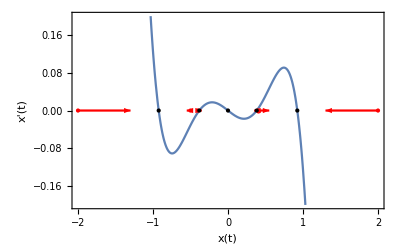

```mathematica
Show[Plot[-(1/8)*u+u^3-u^5,{u,-2,2},Frame->{True,True,False,False},PlotRange->{Automatic,{-1/5,1/5}},FrameLabel->{x[t],TraditionalForm[D[x[t],t]]},Epilog->{PointSize[Medium],Point[{{0,0},{Sqrt[(1+Sqrt[1/2])/2],0},{-Sqrt[(1+Sqrt[1/2])/2],0},{Sqrt[(1-Sqrt[1/2])/2],0},{-Sqrt[(1-Sqrt[1/2])/2],0}}]}],NumberLinePlot[Interval[{-2,Infinity}],{x,-2,-1.3},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,-0.5}],{x,-0.55,-0.5},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-0.4,Infinity}],{x,-0.4,-0.35},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,0.4}],{x,0.35,0.4},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{0.4,Infinity}],{x,0.4,0.55},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,2}],{x,1.3,2},PlotStyle->Red,Spacings->0]]
```

Como en el análisis anterior, cuando , sólo sobreviven el punto de equilibrio cero, y dos puntos de equilibrio diferentes de cero. Mediante los mismos argumentos anteriores, en el primer punto de equilibrio distinto de cero, la función debe cruzar de arriba a abajo (estable), en el cero debe cruzar de abajo hacia arriba (inestable), y en el último punto de equilibrio, debe cruzar de arriba hacia abajo (estable). El diagrama debe verse como:

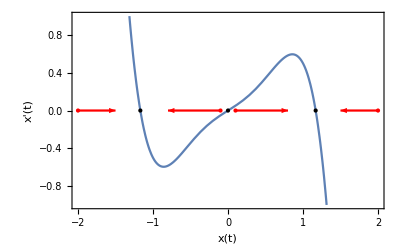

```mathematica
Show[Plot[(1/2)*u+u^3-u^5,{u,-2,2},Frame->{True,True,False,False},PlotRange->{Automatic,{-1,1}},FrameLabel->{x[t],TraditionalForm[D[x[t],t]]},Epilog->{PointSize[Medium],Point[{{0,0},{Sqrt[(1+Sqrt[3])/2],0},{-Sqrt[(1+Sqrt[3])/2],0}}]}],NumberLinePlot[Interval[{-2,Infinity}],{x,-2,-1.5},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,-0.1}],{x,-0.8,-0.1},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{0.1,Infinity}],{x,0.1,0.8},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,2}],{x,1.5,2},PlotStyle->Red,Spacings->0]]
```

## Pregunta IV

Diagramas de bifurcación

Recordamos que, en los diagramas de bifurcación de sistemas en una dimensión, debemos graficar el valor del parámetro contra los puntos de equilibrio, identificando de manera diferente cuando son estables y cuando son inestables. Empezamos calculando los puntos de equilibrio:



Vemos que no hay puntos de equilibrio cuando


tenemos sólo un punto de equilibrio cuando

y dos puntos de equilibrio en cualquier otro caso.
Calculamos la estabilidad de los equilibrios cuando existen. 

Vemos entonces que el punto de equilibrio con signo positivo (el mayor de ambos), es siempre estable, y el que tiene signo negativo (el menor de ambos) es siempre inestable. Cuando sólo hay un punto de equilibrio no se puede determinar la estabilidad, porque es un punto de bifurcación.
Finalmente, para dibujar el diagrama de bifurcación, vems que el lado derecho de la ecuación es una parábola invertida, desplazada por . Calculamos el máximo de la parábola para saber qué pasa durante la bifurcación:


Y calculamos la altura de este máximo

Vemos que si , entonces . Recordamos que las bifurcaciones en una dimensión se dan cuando la función se vuelve tangente al eje , por lo que para  no hay bifurcaciones, pues el máximo, que sería el único punto que podría ser tangente al eje (por tener pendiente cero), siempre está por arriba del eje. Con esta información ya podemos dibujar los diagramas de bifurcación:
Si , entonces necesariamente , tenemos dos puntos de equilibrio que no cambian de estabilidad, el de la izquierda inestable, y el de la derecha estable, por lo que debe verse como dos líneas, la de arriba continua y la de abajo punteada:

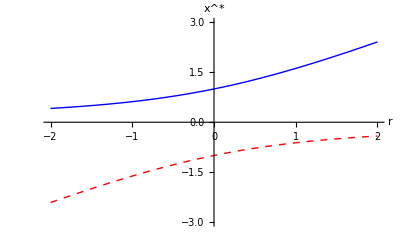

```mathematica
Show[{Plot[(r+Sqrt[r^2+4])/2,{r,-2,2},AxesLabel->{r,SuperStar[x]},PlotRange->{Automatic,{-3,3}},PlotStyle->{Blue,Thick}],Plot[(r-Sqrt[r^2+4])/2,{r,-2,2},AxesLabel->{r,SuperStar[x]},PlotRange->{Automatic,{-3,3}},PlotStyle->{Red,Thick,Dashed}]}]
```

Si , entonces tenemos un solo punto de equilibrio cuando , pero en todos los otros casos tenemos dos puntos de equilibrio. Además, en este caso, uno de los puntos de equilbrio siempre es

Tenemos dos puntos de equilibrio que siempre existen y que, para cierto parámetro, chocan uno con otro. Es una bifurcación transcrítica. Además, en este caso, la ecuación se reduce a la forma normal de la bifurcación trasncrítica, así que ya deberíamos saber que su driagrama de bifurcación se ve como dos lineas que se cortan. Eso sí, siempre la línea de más abajo es inestable y la de más arriba es estable. En este caso se ve como:

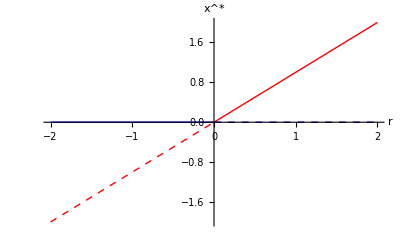

```mathematica
Show[{Plot[0,{r,-2,0},PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-2,2},{-2,2}}],Plot[0,{r,0,2},PlotStyle->{Blue,Thick,Dashed},AxesLabel->{r,SuperStar[x]},PlotRange->{{-2,2},{-2,2}}],Plot[r,{r,-2,0},PlotStyle->{Red,Thick,Dashed},AxesLabel->{r,SuperStar[x]},PlotRange->{{-2,2},{-2,2}}],Plot[r,{r,0,2},PlotStyle->{Red,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-2,2},{-2,2}}]}]
```

Si , entonces tenemos un punto de equilibrio cuando . Vemos que esto se da cuando 


Lo cual está bien definido porque  es negativo. Por lo tanto, deben haber dos valores de  en el diagrama de bifurcación donde hay un sólo punto de equilibrio. Vemos entonces que no hay puntos de equilibrio cuando




Recordando que cuando hay destrucción o creación de puntos de equilibrio corresponde a una bifurcación de silla-nodo, y que el diagrama de bifurcación se ve como una parábola horizontal, las condiciones anteriores quieren decir que el diagrama de bifurcación consiste en dos parábolas, con vértices en , la de la izquierda abriendo a la izquierda (donde existen dos puntos de equilibrio porque ), y la de la derecha abriendo hacia la derecha (donde se cumple la condición de existencia ). El diagrama de bifurcación debe verse como:

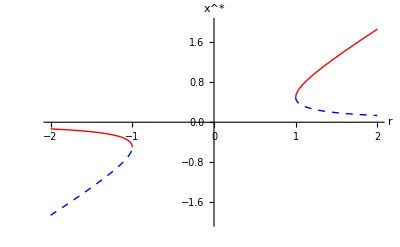

```mathematica
Show[{Plot[(r+Sqrt[r^2-1])/2,{r,-2,-1},PlotStyle->{Red,Thick},PlotRange->{{-2,2},{-2,2}},AxesLabel->{r,SuperStar[x]}],Plot[(r-Sqrt[r^2-1])/2,{r,-2,-1},PlotStyle->{Blue,Thick,Dashed}],Plot[(r-Sqrt[r^2-1])/2,{r,1,2},PlotStyle->{Blue,Thick,Dashed}],Plot[(r+Sqrt[r^2-1])/2,{r,1,2},PlotStyle->{Red,Thick}]}]
```

Espacio de parámetros

El espacio de parámetros que se nos pide es fácil, pues en el inciso anterior ya vemos que 
1. Si  no hay bifurcaciones
2. Si  hay una bifurcación transcrítica
3. Si  hay dos bifurcaciones de silla-nodo.
Por lo tanto, sólo hay que dibujar el espacio con la línea recta  e indicar lo que pasa arriba, en y debajo de ella:

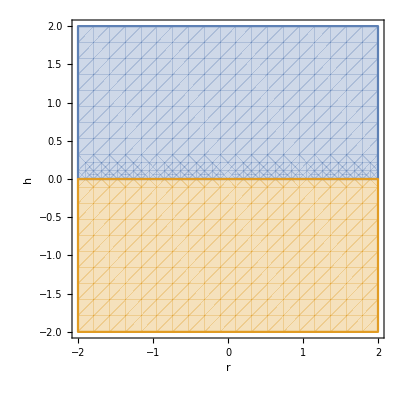

```mathematica
RegionPlot[{h>0,h<0},{r,-2,2},{h,-2,2},FrameLabel->{r,h}]
```

En la línea recta del medio hay que indicar que hay bifurcación trasncrítica, en el área naranja hay que indicar que hay dos bifurcaciones de silla-nodo, y en el área azul indicar que no hay bifurcaciones.
Un espacio de parámetros más completo, que resultaría en puntos extra, sería hacerlo como hicimos en clase, indicando cuantos puntos de equilibrio hay y qué bifurcaciones ocurren. Esto sería de la siguiente forma

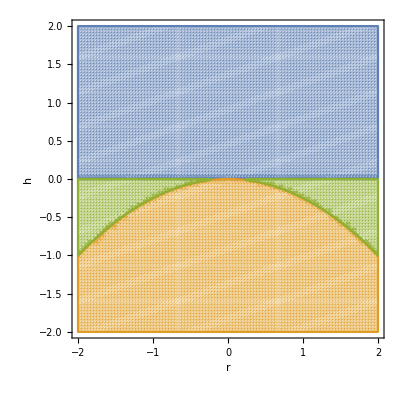

```mathematica
RegionPlot[{h>0,(h<0&&h<-(r^2)/4),(h<0&&h>-(r^2)/4)},{r,-2,2},{h,-2,2},FrameLabel->{r,h},PlotPoints->100]
```

En este caso habría que indicar lo siguiente: región azul: dos puntos de equilibrio; región verde: dos puntos de equilibrio; región naranja: ningún punto de equilibrio; línea recta en cero: bifurcación de punto silla con dos puntos de equilibrio; parábola: bifurcaciones de silla-nodo con un punto de equilibrio; intersección de la parábola con el cero: un punto de equilibrio con bifurcación transcrítica.

## Parcial III

## Pregunta I

Calculamos los puntos de equilibrio de la ecuación. De la segunda ecuación obtenemos




Sustituyendo en la primera ecuación, vemos que  no puede ser solución de equilibrio a menos de que . Sustituyendo la segunda ecuación en el último término de la ecuación obtenemos



y, sustituyendo en la condición de la primera ecuación, obtenemos

.
Sólo tenemos un punto de equilibrio, así que no puede haber bifurcaciones transcríticas, de silla-nodo, ni de tridente. Podría haber una bifurcación de Hopf si este único punto de equilibrio tiene eigenvalores complejos y cambian de tener parte real positiva a negativa. Calculamos la matriz Jacobiana para comprobarlo:

```mathematica
J1={{D[a-(b+1)*x+y*x^2,x],D[a-(b+1)*x+y*x^2,y]},{D[b*x-y*x^2,x],D[b*x-y*x^2,y]}}
```

{{-1-b+2 x y,x^2},{b-2 x y,-x^2}}

```mathematica
MatrixForm[J1]
```

(-1-b+2 x y | x^2
b-2 x y | -x^2)

Evaluamos en el punto de equilibrio:

```mathematica
MatrixForm[FullSimplify[J1/.{x->a,y->b/a}]]
```

(-1+b | a^2
-b | -a^2)

Si los eigenvalores son complejos, la traza es proporcional a la parte real (por un factor de un medio). En este caso la traza es

La cual cambiaría de positiva a negativa si


Sólo basta comprobar en qué rango de parámetros los eigenvalores son complejos. Esto sucede cuando . En este caso el determinante es

```mathematica
Det[J1/.{x->a,y->b/a}]
```

a^2

Entonces necesitamos que




Sólo basta examinar si esta condición se cumple cuando la traza cambia de positiva a negativa, es decir cuando . Sustituimos y obtenemos


Esto se cumple, así que podemos concluir que hay una bifurcación de Hopf en el sistema. Para saber qué tipo de bifurcación de Hopf específicamente (super-, subcrítica o degenerada) tendríamos que mostrar que hay un centro en el punto de bifurcación (para la degenerada), o que existe un ciclo límite cuando el punto de equilibrio es estable (Hopf subcrítica), o que existe cuando es inestable (Hopf supercrítica). En este caso en particular, la bifurcación es supercítica, como se puede ver debajo (no necesario para el examen):

```mathematica
sol=NDSolve[{x'[t]==2-6.05*x[t]+y[t]*x[t]^2,y'[t]==5.05*x[t]-y[t]*x[t]^2,x[0]==2.2,y[0]==2.6},{x,y},{t,0,100}];
```

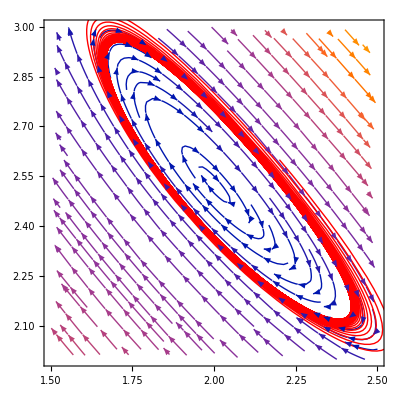

```mathematica
Show[{StreamPlot[{2-6.05*x+y*x^2,5.05*x-y*x^2},{x,1.5,2.5},{y,2,3}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotStyle->{Red,Thick}]}]
```

```mathematica
sol=NDSolve[{x'[t]==2-5.95*x[t]+y[t]*x[t]^2,y'[t]==4.95*x[t]-y[t]*x[t]^2,x[0]==2.2,y[0]==2.6},{x,y},{t,0,100}];
```

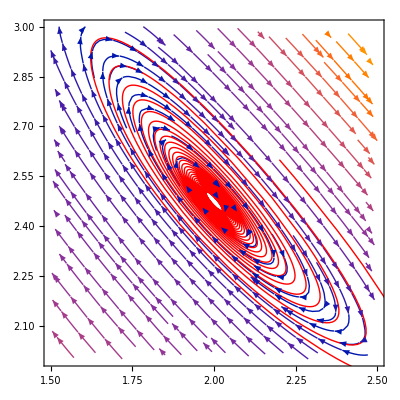

```mathematica
Show[{StreamPlot[{2-5.95*x+y*x^2,4.95*x-y*x^2},{x,1.5,2.5},{y,2,3}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotStyle->{Red,Thick}]}]
```

## Pregunta II

El sistema está en coordenadas polares por lo que la ecuación  sólo indica que las soluciones giran en dirección antihoraria. Las bifurcaciones dependen sólo de la ecuación , el cual no depende de , por lo que podemos tratarlo como un sistema unidimensional. Los puntos de equilibrio de este sistema corresponden a



El primero nos informa que el punto de equilibrio es el origen. El segundo sería un ciclo límite, ya que es una solución que rota a la izquierda con radio constante. Primero, debemos fijarnos que, dado que , entonces este ciclo límite sólo existe cuando . Segundo, recordamos que este punto de equilibrio surge del requerimiento de que 


Graficamente, estos ciclos límite corresponden a la intersección entre la recta  y la curva . Al variar , lo único que estamos haciendo es variar la altura de la recta, por lo que, recordando la forma de la gráfica del seno, es fácil ver que:
1. Cuando  ó  no hay ciclos límite

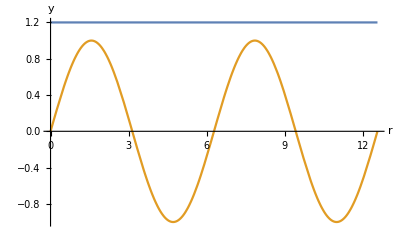

```mathematica
Plot[{1.2,Sin[r]},{r,0,4*Pi},AxesLabel->{r,y}]
```

2. Cuando  hay exactamente una solución de equilibrio cada que , , ó , , ya sea en los máximos o mínimos del seno.

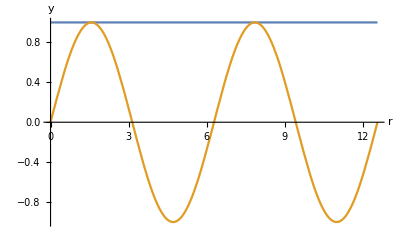

```mathematica
Plot[{1,Sin[r]},{r,0,4*Pi},AxesLabel->{r,y}]
```

3. Cuando , hay un par de soluciones de equilibrio alrededor de cada máximo o mínimo, dependiendo del signo de .

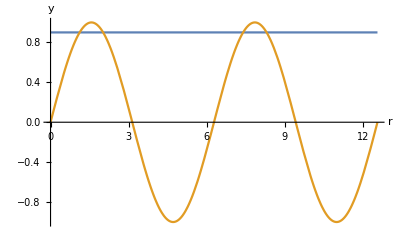

```mathematica
Plot[{0.9,Sin[r]},{r,0,4*Pi},AxesLabel->{r,y}]
```

Por lo tanto, en el sistema unidimensional hay un número infinito, pero numerable, de bifurcaciones de silla-nodo en  y también en . Traduciendo estos resultados al sistema bidimensional completo, tenemos ciclos límite circulares con radios cercanos que se aniquilan en estos valores del parámetro, por lo que tenemos bifurcaciones de silla-nodo de ciclos. Es importante notar que estas son bifurcaciones globales, en lugar de bifurcaciones normales como las que teníamos en otros casos.

## Parcial IV

## Pregunta I

Bifurcación de tridente.

Calculamos lo puntos de equilibrio. Empezamos con la segunda ecuación que dice

Sustituyendo en la primera ecuación, obtenemos

 y 


 y 
Vemos que estos puntos de equilibrio no existen cuando 


Además, cuando , los tres puntos de equilibrio son iguales al . Esto nos dice que debe haber una bifurcación de tridente. Debemos determinar de qué tipo es, calculando la estabilidad. La matriz Jacobiana en este caso está dada por

```mathematica
J2={{D[d*x-x^3-b*y,x],D[d*x-x^3-b*y,y]},{D[x,x],D[x,y]}}
```

{{d-3 x^2,-b},{1,0}}

```mathematica
MatrixForm[J2]
```

(d-3 x^2 | -b
1 | 0)

En el origen, la matriz se reduce a

```mathematica
MatrixForm[J2/.{x->0}]
```

(d | -b
1 | 0)

Cuyo polinomio característico es

```mathematica
CharacteristicPolynomial[J2/.{x->0},λ]
```

b-d λ+λ^2

El criterio de Jury  se traduce a

Resultando en las desigualdades



La segunda desigualdad dice que el cero es estable en el rango de parámetros en el cual los otros puntos de equilibrio no existen, por lo cual  es el punto crítico de una bifurcación de tridente supercrítica.

Bifurcación de flip

Sabemos que la bifurcación de flip ocurre cuando  para alguno de los eigenvalores. Dado el polinomio característico, los eigenvalores están dados por

Sustituimos  y obtenemos

Bifurcación de Hopf

Necesitamos que los eigenvalores sean complejos, y para esto necesitamos que


Sólo necesitamos que  sea suficientemente pequeño. Ahora, suponiendo que estamos en este rango de valors de , sabemos que, si  son las raíces del polinomio característico, entonces éste puede escribirse como

Desarrollando este producto obtenemos


Comparando esta expresión con la obtenida anteriormente para el polinomio característico, vemos que


Si los eigenvalores son complejos, sabemos que son complejos conjugados, por lo que . Entonces tenemos que

Por lo tanto, cuando los eigenvalores están sobre el circulo unitario, su módulo es uno y por lo tanto .

## Pregunta II

En esta pregunta sólo hay que dibujar el cobwebbing y el punto de equilibrio es superestable, así que rápidamente debería converger al punto de equilibrio.

## Pregunta III

Calculamos los puntos de equilibrio. De la segunda ecuación obtenemos


Sustituyendo en la primera ecuación obtenemos

 y con la ecuación anterior, 



 y con la ecuación anterior, 
Vemos que hay dos puntos de equilibrio que siempre existen. Calculamos la matriz Jacobiana:

```mathematica
J3={{D[a*x-y^2,x],D[a*x-y^2,y]},{D[x+a*y,x],D[x+a*y,y]}}
```

{{a,-2 y},{1,a}}

```mathematica
MatrixForm[J3]
```

(a | -2 y
1 | a)

Evaluamos en el primer punto de equilibrio y obtenemos

```mathematica
MatrixForm[J3/.{y->0}]
```

(a | 0
1 | a)

En este caso tenemos eigenvalores repetidos , por lo que el  es estable si , e inestable de otra forma. 
Evaluando el segundo punto de equilibrio encontramos

```mathematica
MatrixForm[J3/.{y->-(1-a)^2}]
```

(a | 2 (1-a)^2
1 | a)

Vemos que  y  y obtenemos el polinomio característico

Usando el criterio de Jury  , nos enfocamos en la primera desigualdad 


Usamos la desigualdad con signo negativo



Como , entonces  y la desigualdad nunca se cumple, por lo cual este punto de equilibrio siempre es inestable.